```mathematica
(1/x)/(1/x+1/y)
```

1/(x (1/x+1/y))

```mathematica
Simplify[1/(x (1/x+1/y))]
```

y/(x+y)

```mathematica
(x/N)^n/(k^n+(x/N)^n)
```

(x/N)^n/(k^n+(x/N)^n)

```mathematica
D[(x/N)^n/(k^n+(x/N)^n), x]
```

-(n (x/N)^(-1+2 n))/(N (k^n+(x/N)^n)^2)+(n (x/N)^(-1+n))/(N (k^n+(x/N)^n))

```mathematica
Simplify[-(n (x/N)^(-1+2 n))/(N (k^n+(x/N)^n)^2)+(n (x/N)^(-1+n))/(N (k^n+(x/N)^n))]
```

(k^n n (x/N)^n)/(x (k^n+(x/N)^n)^2)

```mathematica
mat={{-b*e,0,-b*s},{b*e,-t*g,b*s},{0,t*g,-a}}
```

{{-b e,0,-b s},{b e,-g t,b s},{0,g t,-a}}

```mathematica
Eigenvalues[mat]
```

{Root[a b e g t+(a b e+a g t+b e g t-b g s t) #1+(a+b e+g t) #1^2+#1^3&,1],Root[a b e g t+(a b e+a g t+b e g t-b g s t) #1+(a+b e+g t) #1^2+#1^3&,2],Root[a b e g t+(a b e+a g t+b e g t-b g s t) #1+(a+b e+g t) #1^2+#1^3&,3]}

```mathematica
CharacteristicPolynomial[mat,l]
```

b g l s t+(-a-l) (b e l+l^2+b e g t+g l t)

```mathematica
Simplify[b g l s t+(-a-l) (b e l+l^2+b e g t+g l t)]
```

b g l s t-(a+l) (b e+l) (l+g t)

```mathematica
Collect[b g l s t-(a+l) (b e+l) (l+g t),l]
```

-l^3-a b e g t+l^2 (-a-b e-g t)+l (-a b e-a g t-b e g t+b g s t)

```mathematica
Solve[-l^3-a b e g t+l^2 (-a-b e-g t)+l (-a b e-a g t-b e g t+b g s t)==0,l]
```

{{l→1/3 (-a-b e-g t)+(2^(1/3) (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2))/(3 (2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3))-1/(3 2^(1/3))(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3)},{l→1/3 (-a-b e-g t)-((1+ⅈ √3) (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2))/(3 2^(2/3) (2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3))+1/(6 2^(1/3))(1-ⅈ √3) (2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3)},{l→1/3 (-a-b e-g t)-((1-ⅈ √3) (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2))/(3 2^(2/3) (2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3))+1/(6 2^(1/3))(1+ⅈ √3) (2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3+√(4 (-a^2+a b e-b^2 e^2+a g t+b e g t-3 b g s t-g^2 t^2)^3+(2 a^3-3 a^2 b e-3 a b^2 e^2+2 b^3 e^3-3 a^2 g t+12 a b e g t-3 b^2 e^2 g t+9 a b g s t+9 b^2 e g s t-3 a g^2 t^2-3 b e g^2 t^2+9 b g^2 s t^2+2 g^3 t^3)^2))^(1/3)}}

```mathematica
(S/N)(N-ln(S/N))
```

(S (N-(ln S)/N))/N

```mathematica
D[(S (N-(ln S)/N))/N, S]
```

-(ln S)/N^2+(N-(ln S)/N)/N

```mathematica
Expand[-(ln S)/N^2+(N-(ln S)/N)/N]
```

1-(2 ln S)/N^2

```mathematica
(2*Log[999999999999])/(999999999999^2)
```

(2 Log[999999999999])/999999999998000000000001

```mathematica
N[(2 Log[999999999999])/999999999998000000000001]
```

5.5262×10^-23

```mathematica
N[(2 Log[79999])/6399840001]
```

3.52814×10^-9

```mathematica
N[(2 Log[7])/49]
```

0.0794249

```mathematica
-Log[S/N]
```

-Log[S/N]

```mathematica
D[-Log[S/N], S]
```

-1/S

```mathematica
Log[(N-x)/N]
```

Log[(N-x)/N]

```mathematica
D[Log[(N-x)/N], x]
```

-1/(N-x)

```mathematica
Simplify[-1/(N-x)]
```

1/(-N+x)

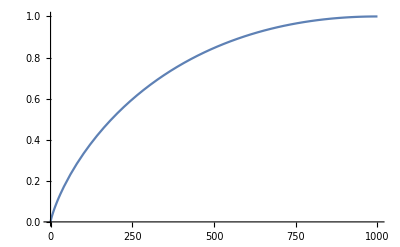

```mathematica
Plot[(S/1000)*(1-Log[S/1000]),{S,0,1000}]
```

```mathematica
V=Log[(N-x)/N]
```

Log[(N-x)/N]